## Common

```mathematica
Needs["PlotLegends`"]
```

```mathematica
readRunFitness[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
noHeaderData = Rest[allData];
data = noHeaderData⟦All,2;;⟧;
{data,noHeaderData⟦All,1⟧, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
readRunEvaluationInfo[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
data = Rest[allData];
{data,Max/@data, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
enlarge[list_, fill_, stat_]:=list~Join~Array[fill&,Max[Length/@stat]-Length[list]]
```

```mathematica
enlarge[list_, fill_, stat_, len_]:=list~Join~Array[fill&,len-Length[list]]
```

This function reads single stat for all experiment runs by multiple parameters/methods. Typical use for "experiments_???.txt" file.

```mathematica
readFinalStats[names_List,statName_]:=
Module[{allData},
allData = ImportString[Import[#],"TSV"]&/@names;
allData⟦#⟦1⟧,2;;,#⟦3⟧⟧&/@Position[allData,statName]
]
```

Reads all stat names from multiple parameters/methods. Returns their intersection.

```mathematica
readFinalStatNames[names_List]:=
Module[{allData},
Flatten[Intersection[(ImportString[Import[#],"TSV"]&/@names)⟦All,1,All⟧]]
]
```

```mathematica
listAllExperimentFiles[dirs_List]:=
Flatten[FileNames[RegularExpression["experiments\\_\\d\\d\\d\\.txt"],{"/Users/drchaj1/java/exp/"<>#}]&/@dirs]
```

## Fitness of a Single Run

```mathematica
{data, bsf, avg, med, min}=readRunFitness["~/java/exp/results/run_001_001_FITNESS.txt"];
```

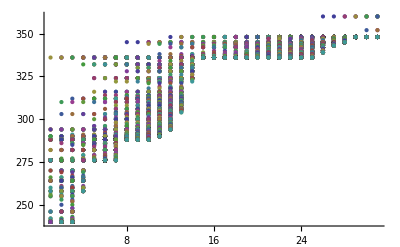

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

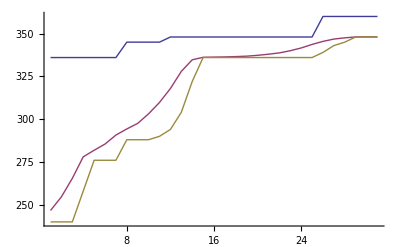

```mathematica
ListLinePlot[{bsf, avg, min}, PlotRange->All]
```

## Fitness over Multiple Runs

```mathematica
bsfAvg = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/results"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

161

```mathematica
enlarge[list_]:=list~Join~Array[Max[bsfAvg]&,Max[Length/@bsfAvg]-Length[list]]
```

```mathematica
bsfAvg=Mean[(enlarge/@bsfAvg)];
```

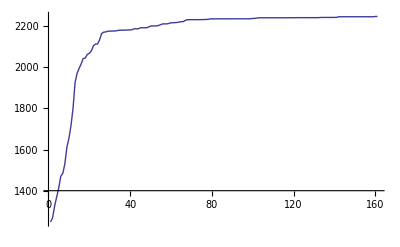

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```

## Evaluation of a Single Run

```mathematica
{data, max, avg, med, min}=readRunEvaluationInfo["~/java/exp/results/run_001_001_AVG_DISTANCE.txt"];
```

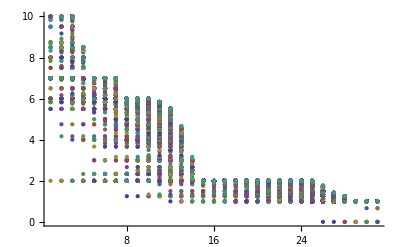

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

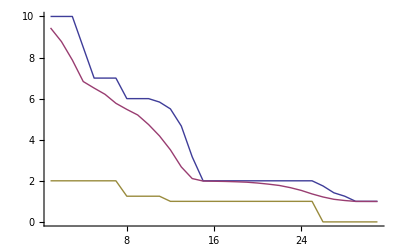

```mathematica
ListLinePlot[{max, avg, min}, PlotRange->All]
```

## Evaluation over Multiple Runs

```mathematica
bsfAvg = (readRunEvaluationInfo[#]⟦5⟧&/@FileNames["run_001*AVG_DISTANCE.txt",{"~/java/exp/results"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

161

```mathematica
bsfAvg=Mean[enlarge[#,Min[bsfAvg], bsfAvg]&/@bsfAvg];
```

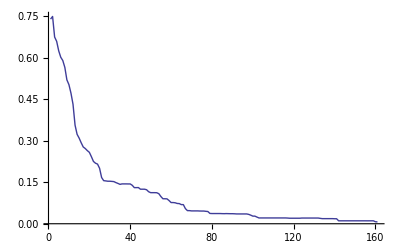

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```

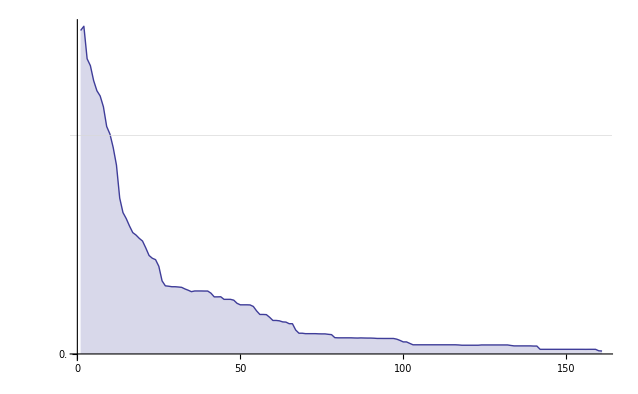

```mathematica
Show[ListLinePlot[{bsfAvg[[1;;]]}, PlotRange->All, Ticks->{Range[0,300, 50],Range[0,25, 0.5]},Filling->Axis,AxesOrigin->{0,0}], GridLines->{None, {0.5}}]
```

## Evaluation over Multiple Methods

```mathematica
singleMethod[methodDir_, variable_, column_] :=
Module[{stat},
stat=(readRunFitness[#]⟦column⟧&/@(Complement[FileNames["run_001*"<>variable<>".txt",{"~/java/exp/results/"<>methodDir}],FileNames["run_001*GENERALIZATION*.txt",{"~/java/exp/results/"<>methodDir}]]));
Mean[enlarge[#,Max[#], stat]&/@stat]
]
```

```mathematica
singleMethodGeneralization[methodDir_, variable_] :=
Module[{stat},
stat = Sequence@@Flatten[#,{3}]&@(ImportString[Import[#],"TSV"]&/@
Intersection[FileNames["run_001*"<>variable<>".txt",{"~/java/exp/results/"<>methodDir}],FileNames["run_001*GENERALIZATION*.txt",{"~/java/exp/results/"<>methodDir}]]);
Mean[enlarge[#,Min[#], stat]&/@stat]
]
```

```mathematica
singleMethodDiversity[methodDir_, variable_] :=
Module[{stat},
stat = Sequence@@Flatten[#,{3}]&@(ImportString[Import[#],"TSV"]&/@
FileNames["run_001_*"<>variable<>"*.txt",{"~/java/exp/results/"<>methodDir}]);
Rescale[Mean[enlarge[#,Mean[#], stat]&/@stat]];
Mean[enlarge[#,Mean[#], stat]&/@stat]
]
```

```mathematica
multipleMethods[methodDirs_, variable_, column_, generalization_:True] :=
Module[{stats, len},
If[generalization==True,
stats=(singleMethod[#,variable, column]&/@methodDirs)~Join~(singleMethodGeneralization[#,variable]&/@methodDirs),
stats=(singleMethod[#,variable, column]&/@methodDirs)];
len = Max[Length/@stats];
stats=enlarge[#,Min[#], stats, len]&/@stats;
Show[
ListLinePlot[stats, PlotRange->All, Ticks->{Range[0,300, 50],Range[0,25, 0.5]},AxesOrigin->{0,0}, PlotStyle->{Thickness[0.005]},
PlotLegend->methodDirs~Join~(StringJoin[#," G"]&/@methodDirs),
PlotMarkers->Automatic,
LegendPosition->{1.1,-0.4}
], 
GridLines->{None, {0.5}}]
]
```

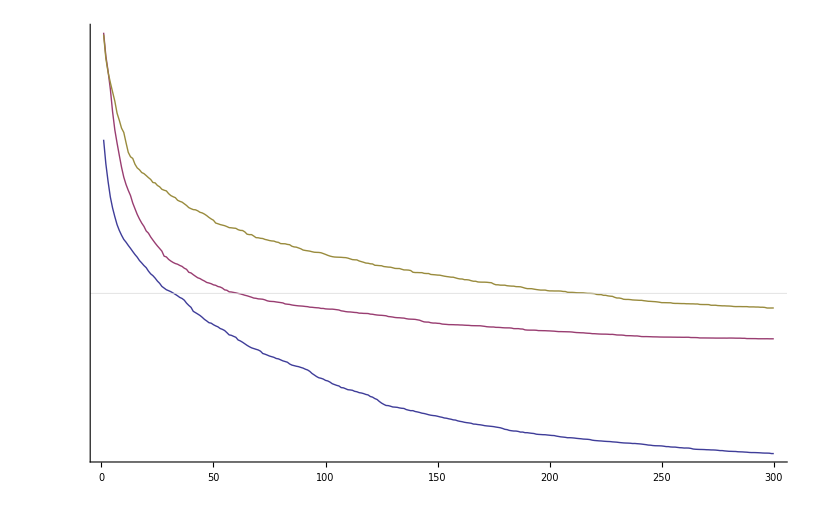

```mathematica
multipleMethods[{"FC_NEAT", "FC_GP", "FC_GPDC"}, "AVG_DISTANCE", 5]
```

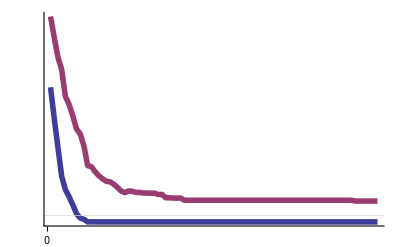

```mathematica
multipleMethods[{"T_NEAT", "T_GP"}, "AVG_DISTANCE", 5]
```

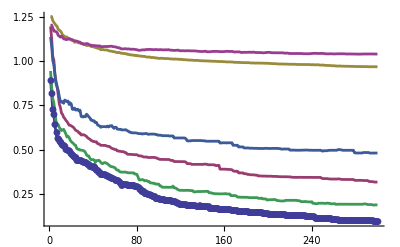

```mathematica
multipleMethods[{"FC_NEAT_7_20", "FC_GP_7_20", "FC_SADE_7_20"}, "AVG_DISTANCE", 5]
```

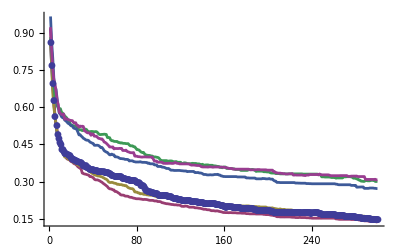

```mathematica
multipleMethods[{"DIV_GP_5_50", "DIV_NEAT_5_50", "DIV_NEAT_5_50_AMP10"}, "AVG_DISTANCE", 5]
```

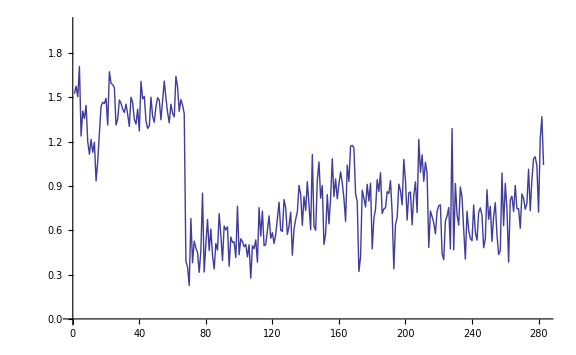

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_5_50"},"DIVERSITY"],PlotRange->{0,2}]
```

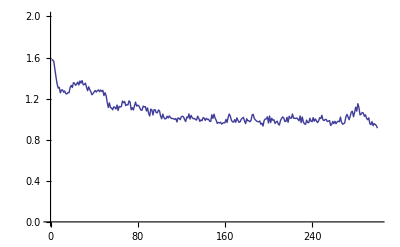

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_5_50"},"DIVERSITY"],PlotRange->{0,2}]
```

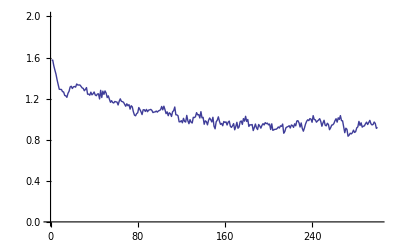

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_5_50_AMP10"},"DIVERSITY"],PlotRange->{0,2}]
```

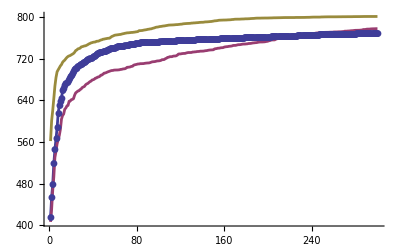

```mathematica
multipleMethods[{"DIV_GP_7_50","DIV_GPC_7_50", "DIV_NEAT_7_50"}, "FITNESS", 2, False]
```

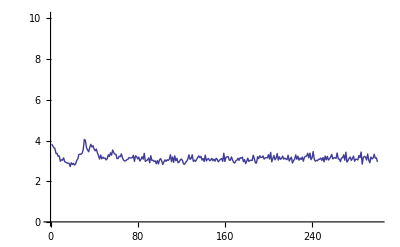

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

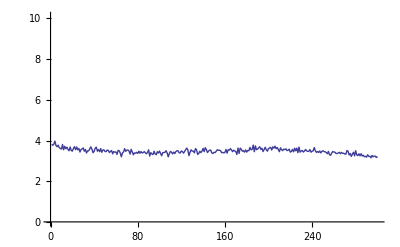

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GPC_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

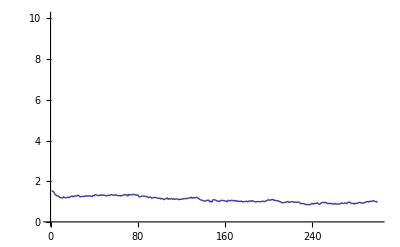

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

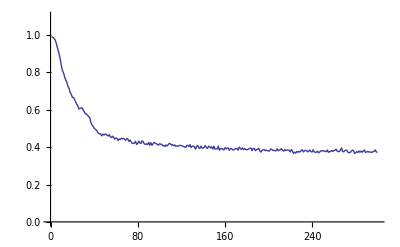

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_7_50"},"G_DIVERSITY"],PlotRange->{0,1.1}]
```

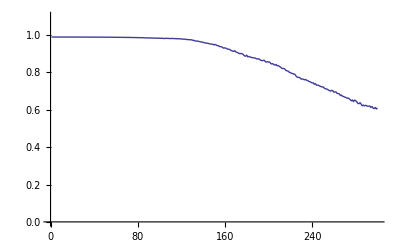

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GPC_7_50"},"G_DIVERSITY"],PlotRange->{0,1.1}]
```

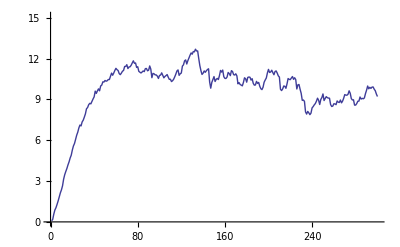

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_7_50"},"G_DIVERSITY"],PlotRange->{0,15.1}]
```

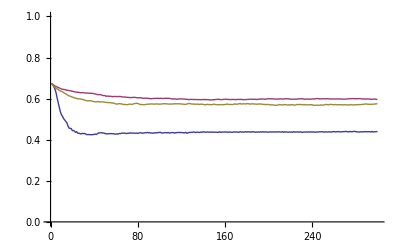

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT"},"G_DIVERSITY"], singleMethodDiversity[{"GEP_ROULETTE"},"G_DIVERSITY"], singleMethodDiversity[{"GEP_TOURNAMENT2"},"G_DIVERSITY"]},PlotRange->{0,1}]
```

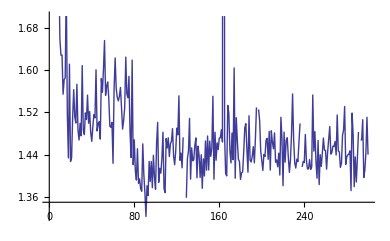

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT"},"P_DIVERSITY"]}]
```

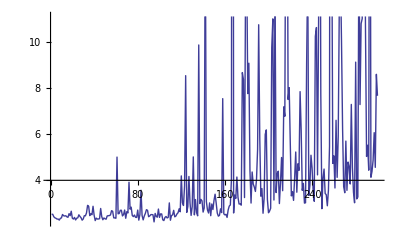

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT2"},"P_DIVERSITY"]}]
```

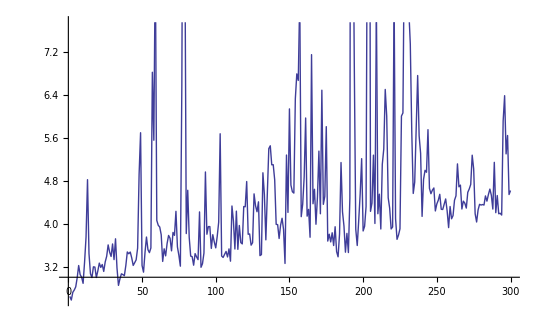

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_ROULETTE"},"P_DIVERSITY"]}]
```

## Final Stats

```mathematica
labels=Flatten[Outer[StringJoin,{"GP_","70_","33_","53_","35_","55_"},{"A","B","C","D","E","F","G","H","I","J","K"}]]
```

{GP_A,GP_B,GP_C,GP_D,GP_E,GP_F,GP_G,GP_H,GP_I,GP_J,GP_K,70_A,70_B,70_C,70_D,70_E,70_F,70_G,70_H,70_I,70_J,70_K,33_A,33_B,33_C,33_D,33_E,33_F,33_G,33_H,33_I,33_J,33_K,53_A,53_B,53_C,53_D,53_E,53_F,53_G,53_H,53_I,53_J,53_K,35_A,35_B,35_C,35_D,35_E,35_F,35_G,35_H,35_I,35_J,35_K,55_A,55_B,55_C,55_D,55_E,55_F,55_G,55_H,55_I,55_J,55_K}

```mathematica
files= listAllExperimentFiles[{"GP1D_SL_1000","GPAT1D_SL_70_1000","GPAT1D_SL_1000"}]
```

{/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_001.txt,/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_002.txt,/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_003.txt,/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_004.txt,/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_005.txt,/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_006.txt,/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_007.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_001.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_002.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_003.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_004.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_005.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_006.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_007.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_001.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_002.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_003.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_004.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_005.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_006.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_007.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_008.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_009.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_010.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_011.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_012.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_013.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_014.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_015.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_016.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_017.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_018.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_019.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_020.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_021.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_022.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_023.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_024.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_025.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_026.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_027.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_028.txt}

```mathematica
files= listAllExperimentFiles[{"20110726/ERROR_CORRECTED/GPAT2D_EC","SLGPAT2D_33","SLGPAT2D_77"}]
```

{/Users/drchaj1/java/exp/20110726/ERROR_CORRECTED/GPAT2D_EC/experiments_001.txt,/Users/drchaj1/java/exp/20110726/ERROR_CORRECTED/GPAT2D_EC/experiments_002.txt,/Users/drchaj1/java/exp/20110726/ERROR_CORRECTED/GPAT2D_EC/experiments_003.txt,/Users/drchaj1/java/exp/20110726/ERROR_CORRECTED/GPAT2D_EC/experiments_004.txt,/Users/drchaj1/java/exp/20110726/ERROR_CORRECTED/GPAT2D_EC/experiments_005.txt,/Users/drchaj1/java/exp/20110726/ERROR_CORRECTED/GPAT2D_EC/experiments_006.txt,/Users/drchaj1/java/exp/20110726/ERROR_CORRECTED/GPAT2D_EC/experiments_007.txt,/Users/drchaj1/java/exp/20110726/ERROR_CORRECTED/GPAT2D_EC/experiments_008.txt,/Users/drchaj1/java/exp/20110726/ERROR_CORRECTED/GPAT2D_EC/experiments_009.txt,/Users/drchaj1/java/exp/20110726/ERROR_CORRECTED/GPAT2D_EC/experiments_010.txt,/Users/drchaj1/java/exp/20110726/ERROR_CORRECTED/GPAT2D_EC/experiments_011.txt,/Users/drchaj1/java/exp/SLGPAT2D_33/experiments_001.txt,/Users/drchaj1/java/exp/SLGPAT2D_33/experiments_002.txt,/Users/drchaj1/java/exp/SLGPAT2D_33/experiments_003.txt,/Users/drchaj1/java/exp/SLGPAT2D_33/experiments_004.txt,/Users/drchaj1/java/exp/SLGPAT2D_33/experiments_005.txt,/Users/drchaj1/java/exp/SLGPAT2D_33/experiments_006.txt,/Users/drchaj1/java/exp/SLGPAT2D_33/experiments_007.txt,/Users/drchaj1/java/exp/SLGPAT2D_33/experiments_008.txt,/Users/drchaj1/java/exp/SLGPAT2D_33/experiments_009.txt,/Users/drchaj1/java/exp/SLGPAT2D_33/experiments_010.txt,/Users/drchaj1/java/exp/SLGPAT2D_33/experiments_011.txt,/Users/drchaj1/java/exp/SLGPAT2D_77/experiments_001.txt,/Users/drchaj1/java/exp/SLGPAT2D_77/experiments_002.txt,/Users/drchaj1/java/exp/SLGPAT2D_77/experiments_003.txt,/Users/drchaj1/java/exp/SLGPAT2D_77/experiments_004.txt,/Users/drchaj1/java/exp/SLGPAT2D_77/experiments_005.txt,/Users/drchaj1/java/exp/SLGPAT2D_77/experiments_006.txt,/Users/drchaj1/java/exp/SLGPAT2D_77/experiments_007.txt,/Users/drchaj1/java/exp/SLGPAT2D_77/experiments_008.txt,/Users/drchaj1/java/exp/SLGPAT2D_77/experiments_009.txt,/Users/drchaj1/java/exp/SLGPAT2D_77/experiments_010.txt,/Users/drchaj1/java/exp/SLGPAT2D_77/experiments_011.txt}

```mathematica
labels=Range[Length[files]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}

```mathematica
{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}
```

```mathematica
labels={"00","30","50","70","90","03","33","53","73","93","05","35","55","75","95","07","37","57","77","97","09","39","59","79","99"}
```

{00,30,50,70,90,03,33,53,73,93,05,35,55,75,95,07,37,57,77,97,09,39,59,79,99}

```mathematica
labels=Flatten[Transpose[Partition[labels,Length[labels]/6]]]
```

{GP_A,70_A,33_A,53_A,35_A,55_A,GP_B,70_B,33_B,53_B,35_B,55_B,GP_C,70_C,33_C,53_C,35_C,55_C,GP_D,70_D,33_D,53_D,35_D,55_D,GP_E,70_E,33_E,53_E,35_E,55_E,GP_F,70_F,33_F,53_F,35_F,55_F,GP_G,70_G,33_G,53_G,35_G,55_G,GP_H,70_H,33_H,53_H,35_H,55_H,GP_I,70_I,33_I,53_I,35_I,55_I,GP_J,70_J,33_J,53_J,35_J,55_J,GP_K,70_K,33_K,53_K,35_K,55_K}

```mathematica
files=Flatten[Transpose[Partition[files,Length[files]/6]]]
```

{/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_001.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_001.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_001.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_008.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_015.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_022.txt,/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_002.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_002.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_002.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_009.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_016.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_023.txt,/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_003.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_003.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_003.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_010.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_017.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_024.txt,/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_004.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_004.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_004.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_011.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_018.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_025.txt,/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_005.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_005.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_005.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_012.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_019.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_026.txt,/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_006.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_006.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_006.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_013.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_020.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_027.txt,/Users/drchaj1/java/exp/GP1D_SL_1000/experiments_007.txt,/Users/drchaj1/java/exp/GPAT1D_SL_70_1000/experiments_007.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_007.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_014.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_021.txt,/Users/drchaj1/java/exp/GPAT1D_SL_1000/experiments_028.txt}

```mathematica
files=listAllExperimentFiles[labels]
```

{/Users/drchaj1/java/exp/GP_I/experiments_001.txt,/Users/drchaj1/java/exp/GPAT_I/experiments_001.txt,/Users/drchaj1/java/exp/GP_J/experiments_001.txt,/Users/drchaj1/java/exp/GP_K/experiments_001.txt,/Users/drchaj1/java/exp/GPAT_K/experiments_001.txt}

```mathematica
readFinalStatNames[files]
```

{BSF,BSFG,ARITY_BSF,ARITY_LG,CONSTANTS_BSF,CONSTANTS_LG,DEPTH_BSF,DEPTH_LG,LEAVES_BSF,LEAVES_LG,NODES_BSF,NODES_LG,GENERATIONS,EVALUATIONS,MAX_FITNESS,SUCCESS,TIME}

```mathematica
Clear[finalStatsAll];
```

```mathematica
finalStatsAll[files_,methods_,sortBy_:Null,colors_:"Rainbow"]:=
Module[{statNames,statPosition,data,order,labels,labelPlacement,success},
(* Names of all stats. *)
statNames=readFinalStatNames[files];
(* A position of a stat to sort by. *)
statPosition=Flatten[Position[statNames,sortBy]];
data=readFinalStats[files,#]&/@statNames;
(* No sort-by stat given or not existing one given. *)
If[Length[statPosition]==1,
order=Ordering[Median/@data[[statPosition⟦1⟧]]],
order=Range[Length[files]]
];
(* Sort data and labels. *)
data=Part[#,order]&/@data;
labels =methods⟦order⟧;

(* Compute % of sucessful runs *) 
success=N[100*Count[#,"true"]/Length[#]&/@data⟦Sequence@@Flatten[Position[statNames,"SUCCESS"]]⟧];

(* Print them as a table. *)
Print[Grid[Transpose@{{Style["ID",Bold]}~Join~labels,{Style["SUCCESS %",Bold]}~Join~success},Frame->All]];
(* And a bar chart. *)
labelPlacement=Placed[labels,Axis,Rotate[#,Pi/2]&];
Print[BarChart[success,ChartLabels->labelPlacement,ChartStyle->colors,LabelingFunction->Center,ImageSize->1200]];
(* All other stats as box plots.*)
Grid[Transpose[{statNames,
BoxWhiskerChart[#,"Notched",ChartLabels->labelPlacement,ChartStyle->colors,ImageSize->1200]&
/@data
}]]
]
```

```mathematica
colors=Take[{LightRed,LightGreen,LightBlue,LightOrange,LightBrown,LightCyan,LightMagenta},6];
```

ID | SUCCESS %
70_A | 100.
33_A | 100.
53_A | 100.
35_A | 100.
55_A | 100.
70_B | 100.
33_B | 100.
53_B | 100.
35_B | 100.
55_B | 100.
70_C | 100.
33_C | 100.
53_C | 100.
35_C | 100.
55_C | 100.
70_D | 100.
33_D | 100.
53_D | 100.
35_D | 100.
55_D | 100.
70_E | 72.9
33_E | 79.5
53_E | 76.9
35_E | 79.8
55_E | 76.
70_F | 45.2
33_F | 57.4
53_F | 52.6
35_F | 48.7
55_F | 42.3
70_G | 0.1
33_G | 0.
53_G | 0.1
35_G | 0.1
55_G | 0.1

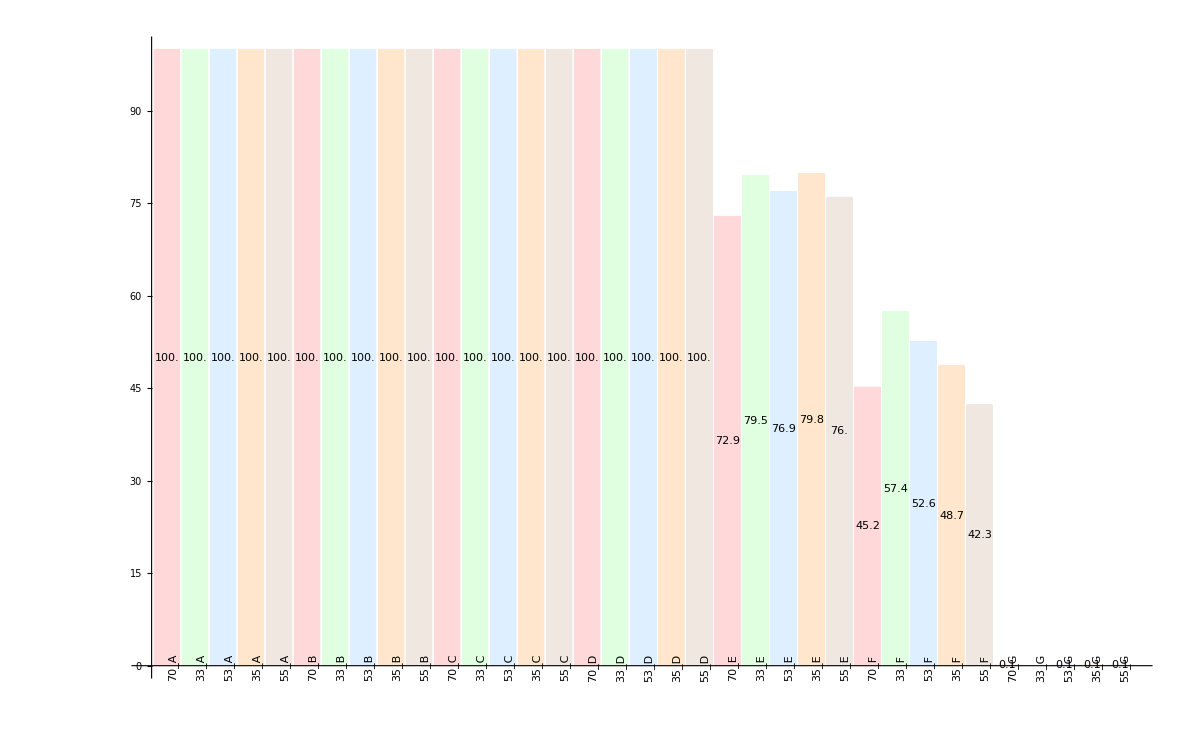

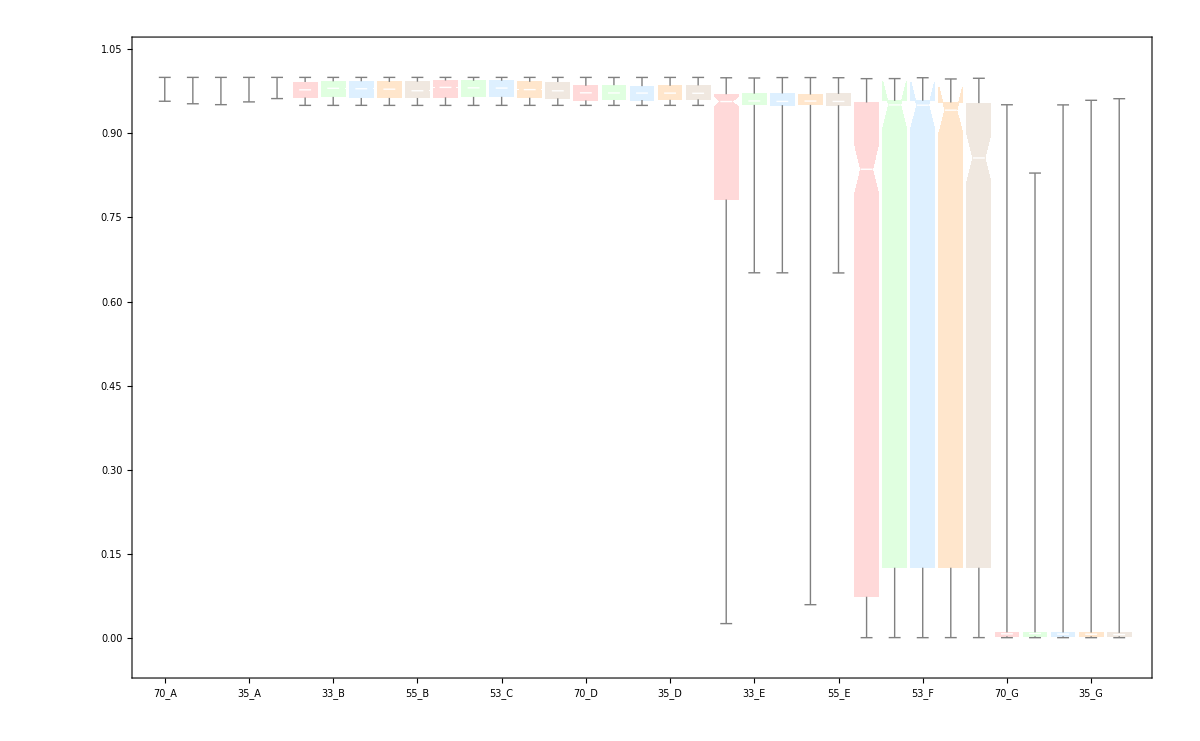
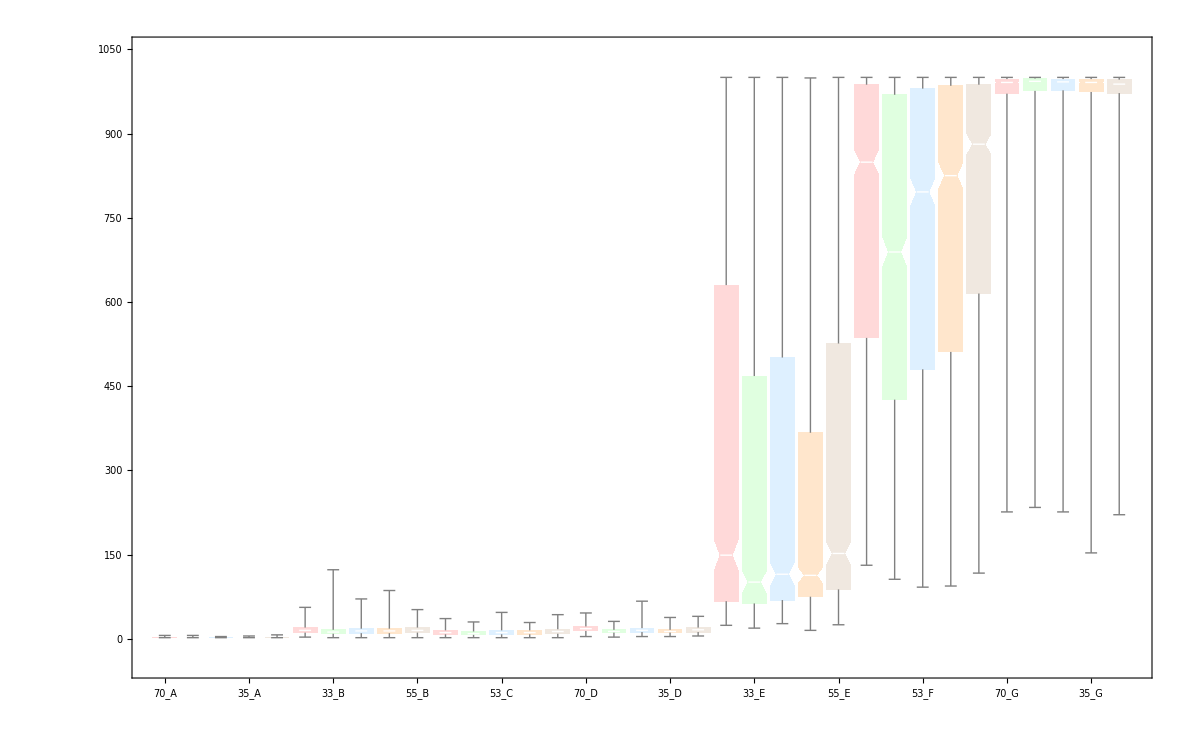
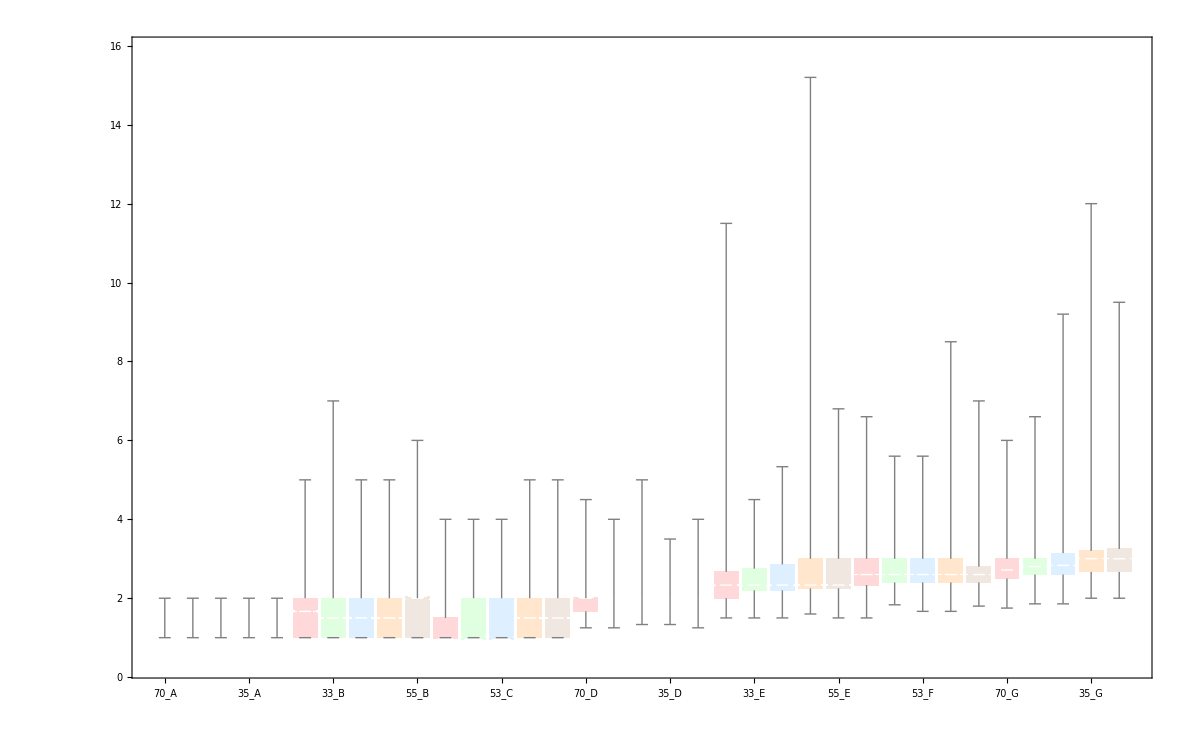
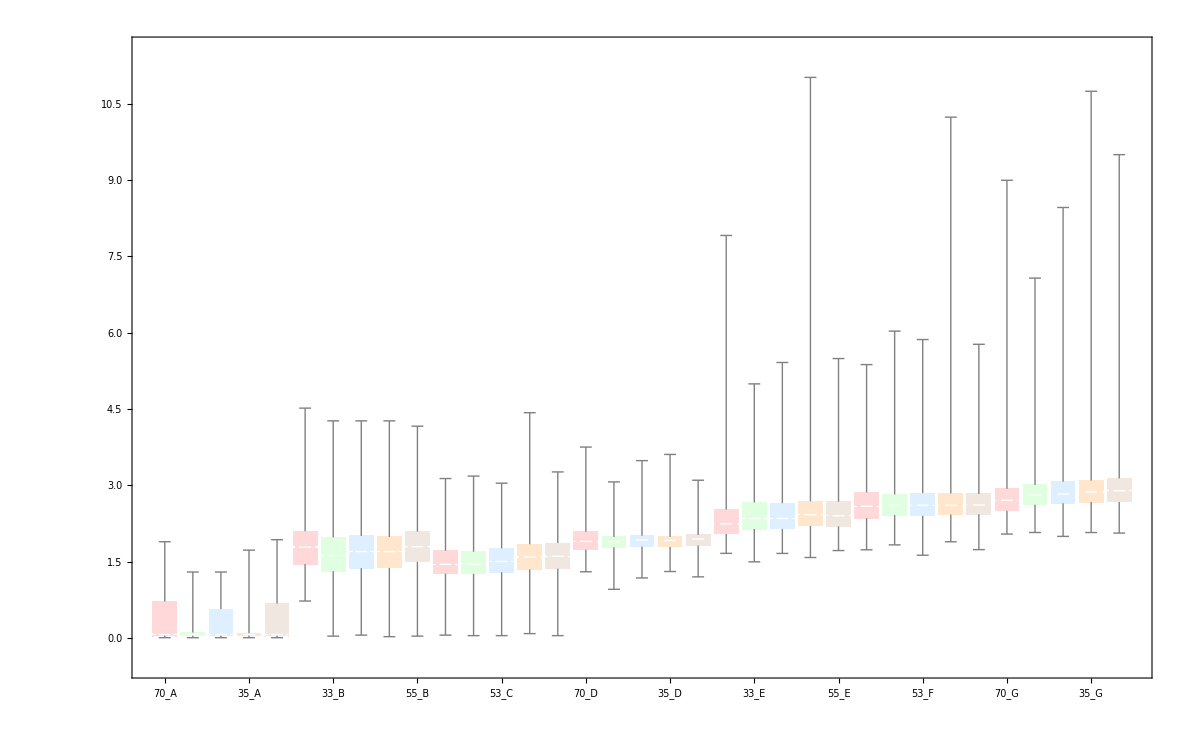
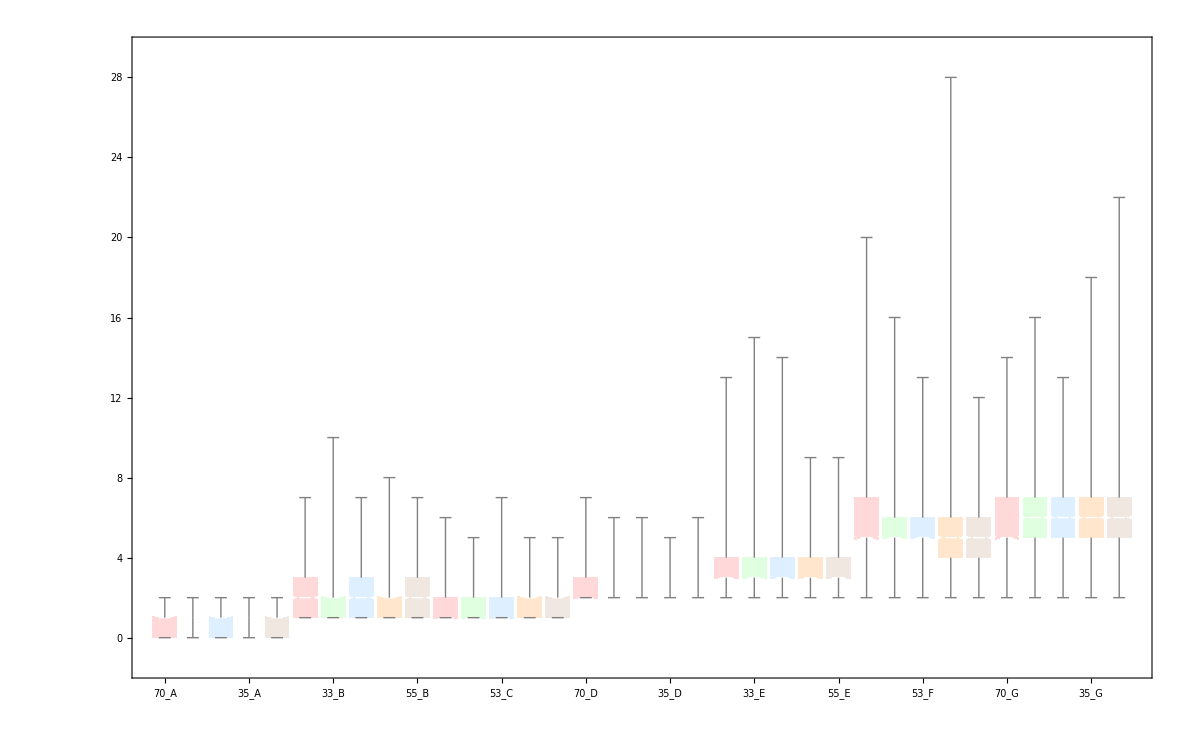
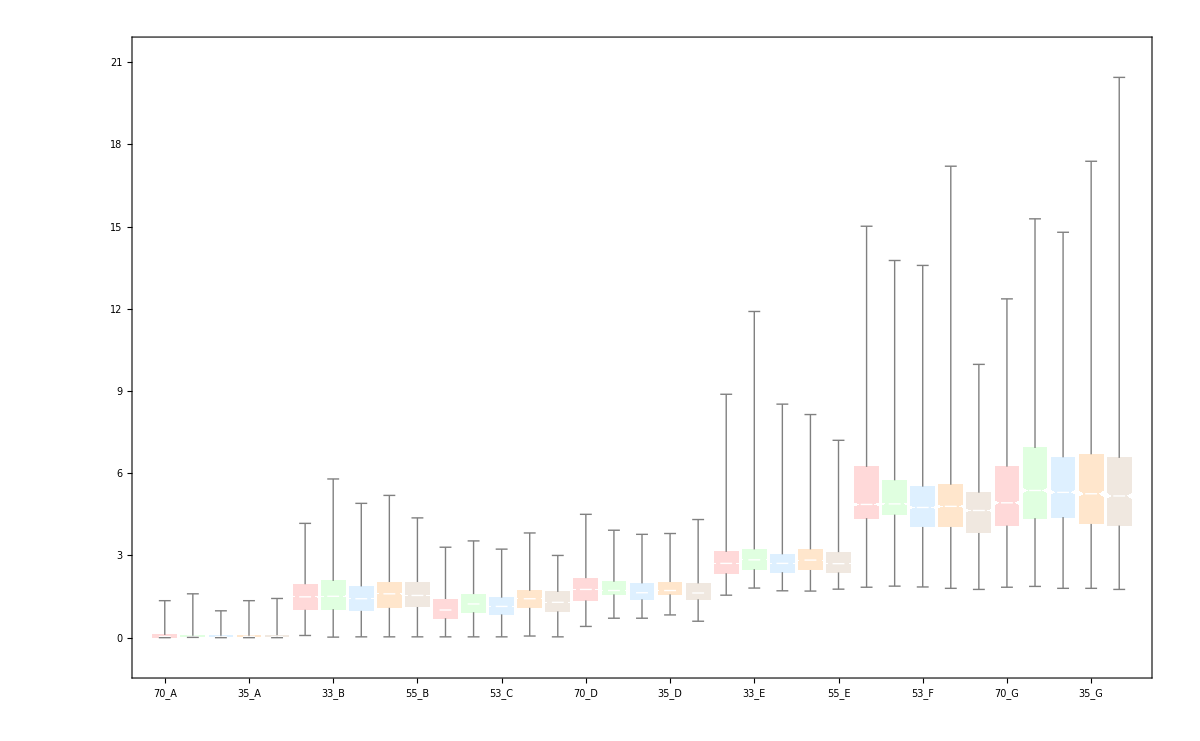
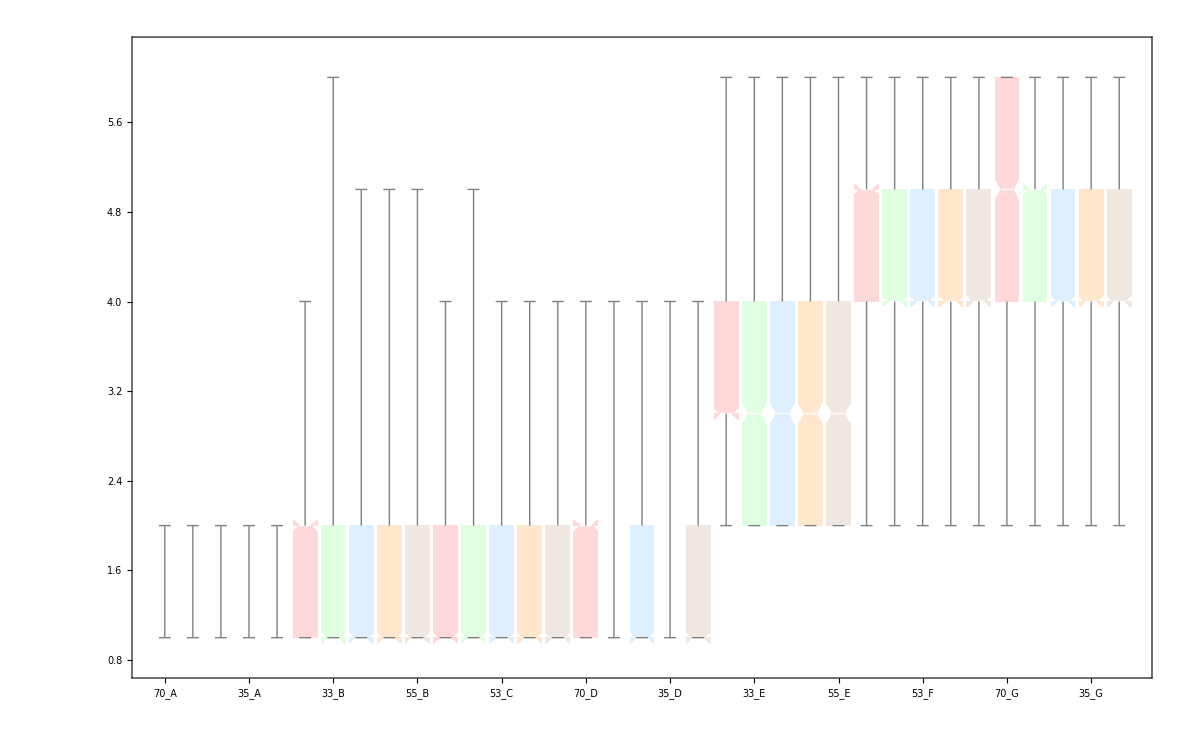
BSF | -Graphics-
BSFG | -Graphics-
ARITY_BSF | -Graphics-
ARITY_LG | -Graphics-
CONSTANTS_BSF | -Graphics-
CONSTANTS_LG | -Graphics-
DEPTH_BSF | -Graphics-
DEPTH_LG | -Graphics-
LEAVES_BSF | -Graphics-
LEAVES_LG | -Graphics-
NODES_BSF | -Graphics-
NODES_LG | -Graphics-
GENERATIONS | -Graphics-
EVALUATIONS | -Graphics-
MAX_FITNESS | -Graphics-
SUCCESS | -Graphics-
TIME | -Graphics-

```mathematica
finalStatsAll[files,labels,Null,colors]
```

```mathematica
1
```